```mathematica
LinguisticAssistant  (*Se puede abrir el menu para datos del mundo real, con Ctrl + = *)
```

```mathematica
Entity["Planet","Mars"]["Image"]
```

-Graphics-

```mathematica
EdgeDetect@-Graphics-
```

-Graphics-

```mathematica
ColorNegate@-Graphics-
```

-Graphics-

```mathematica
EntityValue[Entity["Country","UnitedStates"],"RadioStations"]
```

13769

```mathematica
Entity["Country","China"]["BordersLengths"]
```

{Mongolia→4677. km,Russia→3645. km,India→3380. km,Myanmar→2185. km,Kazakhstan→1533. km,North Korea→1416. km,Vietnam→1281. km,Nepal→1236. km,Kyrgyzstan→858. km,Pakistan→523. km,Bhutan→470. km,Laos→423. km,Tajikistan→414. km,Afghanistan→76. km,Hong Kong→30. km,Macau→0.34 km}

```mathematica
EntityClass["Planet", All]
```

```mathematica
EntityList[%]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

```mathematica
EntityValue[,"Image"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityProperties["Museum"]
```

{administrative division,architect,city,closing date,coordinates,country,founder,latitude,longitude,museum types,name,opening date,opening hours,position,visitors,website}

```mathematica
Entity["Word", "museum"]
```

```mathematica
Entity["Word","museum"]["meaning"]
```

Missing[UnknownProperty,{Word,meaning}]

```mathematica
%["meaning"]
```

Missing[UnknownProperty,{Word,meaning}]

```mathematica
(*Se puede prceder en ingles llano para obtener propiedades de entidades*)
```

```mathematica
Entity["Building", "EiffelTower::5h9w8"][EntityProperty["Building", "Height"]]
```

324. m

```mathematica
Entity["Chemical","Tetrahydrocannabinol"]["MoleculePlot"]
```

-Graphics3D-

```mathematica
ImageCollage[["Image"]]
```

-Graphics-

```mathematica
DominantColors[Entity["Artwork","TheStarryNight::VincentVanGogh"]["Image"]]
```

{RGBColor[0.297103420224274, 0.39748369384299814, 0.5477037839163498],RGBColor[0.1107146308436199, 0.12747658671297116, 0.1127737979377674],RGBColor[0.6281692392913771, 0.6763932236178415, 0.6093323124755855],RGBColor[0.17136551455262033, 0.22704707976824307, 0.4858383895066503],RGBColor[0.6966070912541562, 0.720469801609653, 0.4762123340603765],RGBColor[0.6993331614458606, 0.6273550791543788, 0.2107647020321266]}

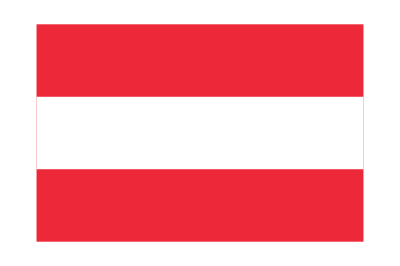
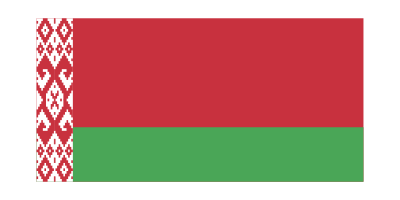
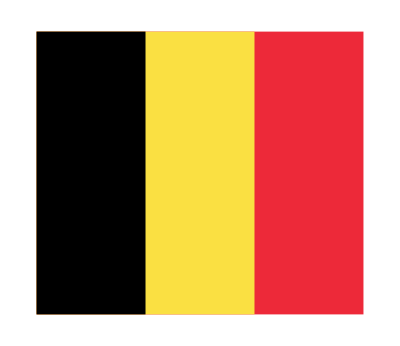
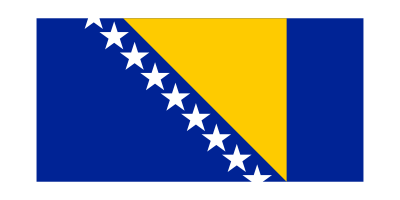
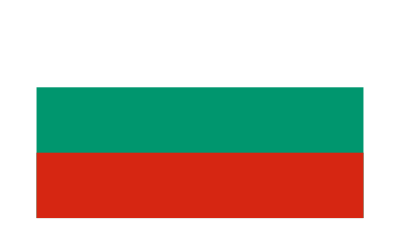
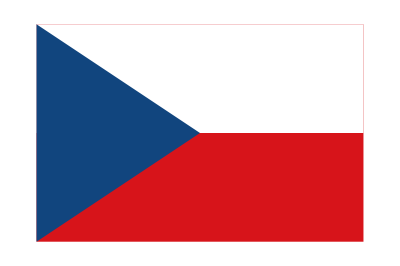
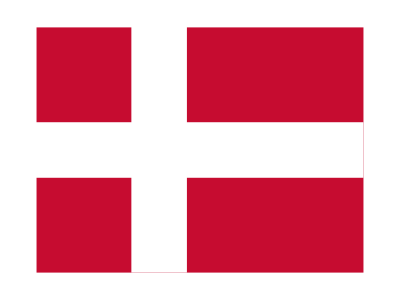
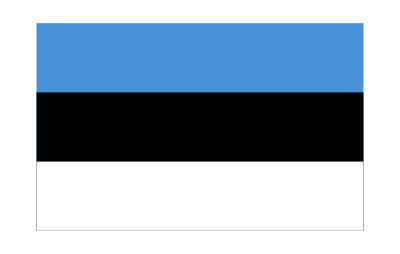


{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityValue[Entity["GeographicRegion","Europe"][EntityProperty["GeographicRegion","Countries"]],"Flag"]
```

```mathematica
ImageCollage@%
```

-Graphics-

```mathematica
EdgeDetect@Entity["Artwork","TheStarryNight::VincentVanGogh"]["Image"]
```

-Graphics-

```mathematica
ColorNegate@Entity["Artwork","MonaLisa::LeonardoDaVinci"]["Image"]
```

-Graphics-

```mathematica
ImageAdd[Entity["Species", "Species:PhascolarctosCinereus"][EntityProperty["Species", "Image"]],Entity["Country","Australia"][EntityProperty["Country","Flag"]]]
```

-Graphics-

```mathematica
Entity["Planet","Mars"]["GravitationalConstantMassProduct"]
```

4.283×10^13 m^3/s^2

```mathematica
x=19 Entity["Planet","Earth"][EntityProperty["Planet","OrbitPeriod"]]/Entity["Planet","Mars"][EntityProperty["Planet","OrbitPeriod"]]
```

10.102

```mathematica
(*Edad terrestre en a;os marcianos*)
```

```mathematica
CurrencyConvert[Quantity[2500, "Yen"],Quantity[, "USDollars"]]
```

22.55 $

```mathematica
CurrencyConvert[Quantity[, "USDollars"],Quantity[, "ChileanPesos"]]
```

680.508 $

```mathematica
total=Quantity[35, "Ounces"]+Quantity[0.25, "ShortTons"]+Quantity[45, "Pounds"]+Quantity[9, "Stones"]
UnitConvert[total] (*Unit Convert asi solito tiene output de SI*)
```

10771. oz

305.353 kg